# 数学建模

导入数据

```mathematica
data=Import["G:\\GitHub Local Repository\\Mathematical-Modeling-Campus-Competition\\2020年兰州大学数学建模竞赛赛题 (1)\\Data.xlsx"];
```

```mathematica
data//Dimensions
```

{2}

```mathematica
train=data[[1,2;;All]];
```

```mathematica
test=data[[2,2;;All]];
```

数据预处理

```mathematica
asso=MapThread[Rule,{train[[All,1;;7]],train[[All,8]]}][[2;;All]];
```

```mathematica
model=Classify[asso,Method->"SupportVectorMachine"];
```

## 探索 7指标分类器

```mathematica
Information[model]
```

Classifier information
Data type | NumericalVector (length: 7)
Classes | ,,0.1.
Accuracy | (91.80.8) %
Method | SupportVectorMachine
Single evaluation time | 6.66 ms/example
Batch evaluation speed | 5.12 examples/ms
Loss | 0.257 ± 0.014
Model memory | 1.21 MB
Training examples used | 19999 examples
Training time | 1 32
 |

```mathematica
model[test[[2]]]
```

1.

## 进行主成分分析

```mathematica
features=train[[All,1;;7]];
```

```mathematica
lables=train[[All,8]];
```

得到降维后的数据

```mathematica
reduced=(KarhunenLoeveDecomposition[Transpose[features]][[1]]//Transpose)[[All,1;;2]];
```

现在要求出主向量

```mathematica
vector=KarhunenLoeveDecomposition[Transpose[features],Standardized->True][[2]]
```

{{0.532456,0.558647,0.489608,0.189288,0.328206,0.0947973,0.110235},{-0.302602,-0.0318648,-0.223899,0.278935,0.364256,0.589206,0.547389},{-0.0739652,0.728162,-0.516356,0.126275,-0.419969,0.0524974,-0.0510952},{-0.59596,0.35595,0.0995157,-0.227029,0.46248,-0.488363,0.0655788},{0.514067,-0.0786769,-0.596697,-0.284208,0.349196,-0.30618,0.277559},{-0.00297143,0.0802815,0.270494,-0.571598,-0.434766,0.0563422,0.633607},{0.00321531,-0.131693,0.0664174,0.641388,-0.241614,-0.552878,0.450338}}

```mathematica
vector2=KarhunenLoeveDecomposition[Transpose[features]][[2]]
```

{{0.532456,0.558647,0.489608,0.189288,0.328206,0.0947973,0.110235},{-0.302602,-0.0318648,-0.223899,0.278935,0.364256,0.589206,0.547389},{-0.0739652,0.728162,-0.516356,0.126275,-0.419969,0.0524974,-0.0510952},{0.59596,-0.35595,-0.0995157,0.227029,-0.46248,0.488363,-0.0655788},{-0.514067,0.0786769,0.596697,0.284208,-0.349196,0.30618,-0.277559},{0.00297143,-0.0802815,-0.270494,0.571598,0.434766,-0.0563422,-0.633607},{0.00321531,-0.131693,0.0664174,0.641388,-0.241614,-0.552878,0.450338}}

```mathematica
vector.(Transpose@features)
```

{{1.66793,1.32634,1.93454,0.473089,0.382777,1.88853,1.77988,0.572647,0.380496,0.402651,19980,1.58351,1.36083,1.54575,0.858486,1.45269,1.64681,1.26729,1.33699,1.53146,1.11805},5,{1}}
 |  |  |  |

对降维后的数据进行画图操作：

```mathematica
po1=Position[lables,x_/;x==1]//Flatten;
```

```mathematica
po2=Position[lables,x_/;x==0]//Flatten;
```

```mathematica
point1=reduced[[po1]];
```

```mathematica
point2=reduced[[po2]];
```

```mathematica
point1//Dimensions
```

{13895,2}

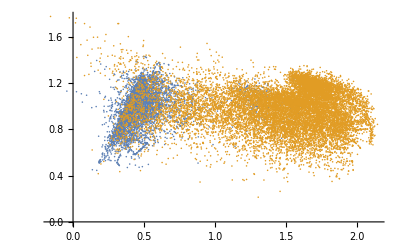

```mathematica
ListPlot[{point2,point1},PlotRange->{Full,All}]
```

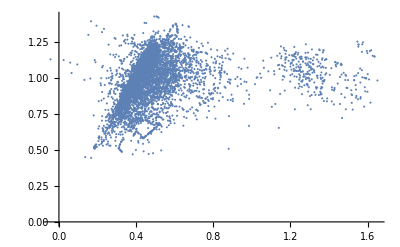

```mathematica
ListPlot[{point2},PlotRange->{Full,All}]
```

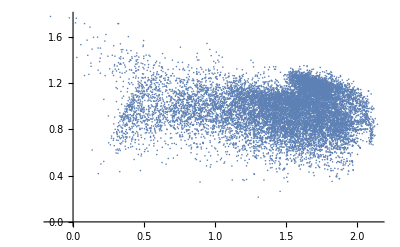

```mathematica
ListPlot[{point1},PlotRange->{Full,All}]
```

```mathematica
asso2=MapThread[Rule,{reduced,lables}];
```

```mathematica
model2=Classify[asso2,Method->{"SupportVectorMachine","KernelType"->"Linear"}];
```

```mathematica
model2//Information
```

Classifier information
Data type | NumericalVector (length: 2)
Classes | ,,0.1.
Accuracy | (92.100.27) %
Method | SupportVectorMachine
Single evaluation time | 5.39 ms/example
Batch evaluation speed | 10.4 examples/ms
Loss | 0.264 ± 0.0084
Model memory | 1.02 MB
Training examples used | 20000 examples
Training time | 1 12
 |

```mathematica
clusters={point1,point2};
```

```mathematica
plota=ListPointPlot3D[Map[Append[#,1]&,clusters,{2}], PlotStyle->{Green,Red}]
```

-Graphics3D-

```mathematica
plotb=Plot3D[{
model2[{x,y},"Probability"->1.],
model2[{x,y},"Probability"->0.]
},
{x,-6,6},{y,-6,6},
 Exclusions->None]
```

-Graphics3D-

```mathematica
Show[plota,plotb,ViewPoint->Above]
```

-Graphics3D-

```mathematica
count[x_,y_][r_,point_]:=(If[(x-r)<#[[1]]<(x+r)&&(y-r)<#[[2]]<(y+r),1,0]&/@point//Total)
```

衬比度

```mathematica
Obvious[x_,y_]:=If[
x≠0||y≠0,Abs@(x-y)/(x+y),0.3
]//N
```

```mathematica
p[r_,h_,point_]:=ParallelTable[{x,y,count[x,y][r,point]},{x,0,2.5,h},{y,0,2,h}];
```

```mathematica
list[r_,h_]:=MapThread[{#1[[1]],#1[[2]],Obvious[#1[[3]],#2[[3]]]}&,{p[r,h,point1],p[r,h,point2]},2];
```

```mathematica
contour=Flatten[list[0.05,0.1],1];
```

```mathematica
contour//Dimensions
```

{546,3}

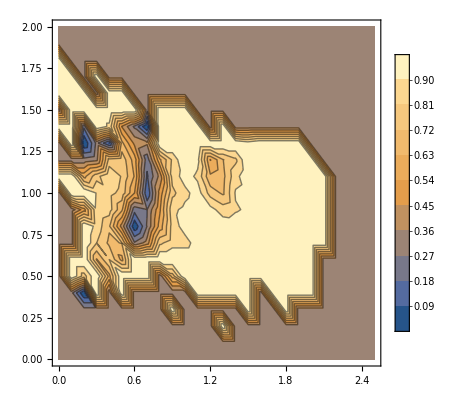

```mathematica
con=ListContourPlot[contour,PlotLegends->Automatic,Contours->10]
```

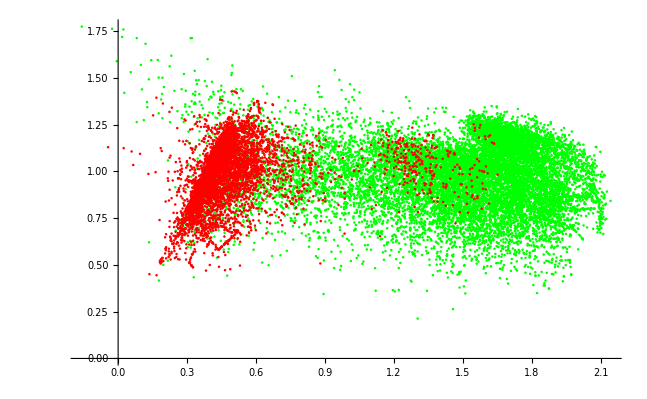

```mathematica
lis=ListPlot[{point1,point2},PlotStyle->{Green,Red}]
```

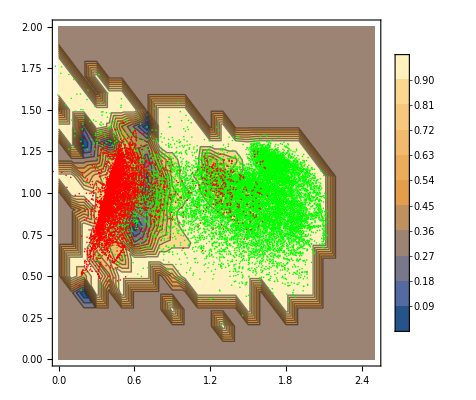

```mathematica
Show[con,lis]
```

```mathematica
train
```

{{0.535424,0.91096,0.524026,0.99252,0.837432,0.895676,0.632646,1.},{0.431184,0.763346,0.350371,0.885103,0.532782,0.926587,0.621668,1.},19997,{0.452727,0.703516,0.397365,0.733164,0.217976,0.456726,0.324843,1.}}
 |  |  |  |

```mathematica
Min/@(train//Transpose)
```

{-0.752723,-0.0626872,-1.26194,0.32084,0.134443,0.183343,0.118308,0.}

```mathematica
Max/@(train//Transpose)
```

{0.965002,0.985052,0.920936,0.999775,0.994328,0.999482,0.847895,1.}

## 对测试集进行降维

```mathematica
Transpose[vector.#&/@test]
```

{{1.72242,1.10616,1.87417,1.27799,0.625463,1.5165,1.58675,1.14584,1.47834,1.27274,4980,1.72001,1.60694,1.66892,0.437771,0.293726,1.95209,1.69612,0.559767,0.59286,0.489688},5,{1}}
 |  |  |  |

```mathematica
features//Dimensions
```

{20000,7}

```mathematica
%//Dimensions
```

{7,5000}

```mathematica
vector//Dimensions
```

{7,7}